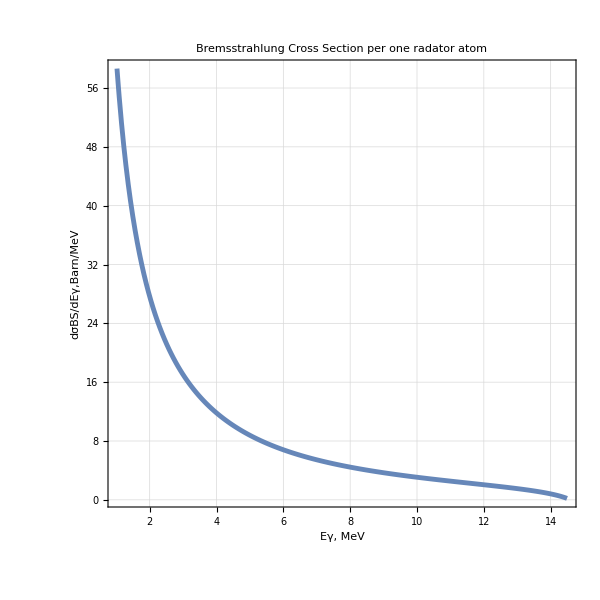

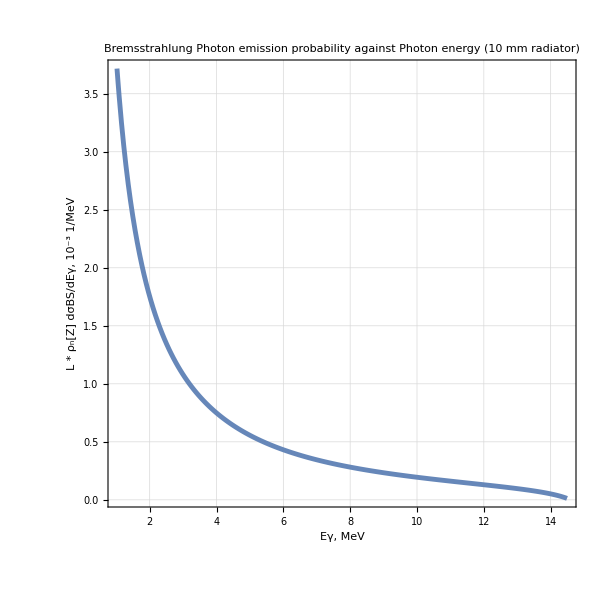

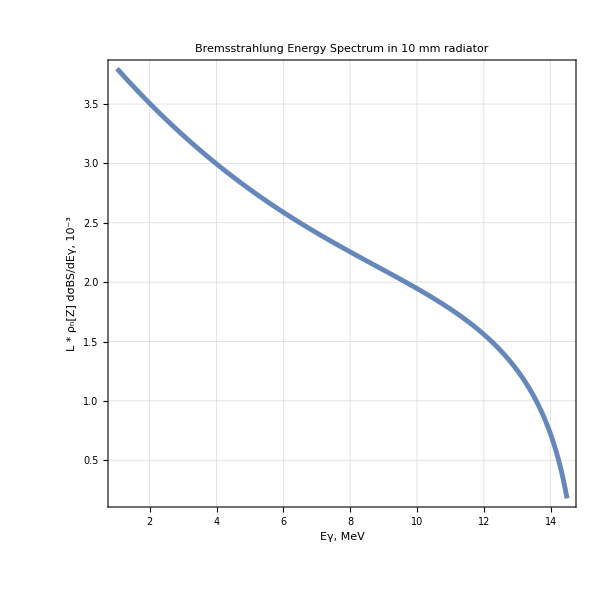

```mathematica
(*Программа производит расчёт спектров тормозного излучения электронов в следующих материалах: C, Al, Si, V, Fe, Ni, Cu, Ge, Ag, W, Pb;
Расчёты проводятся согласно формуле Schiff 
Основаная статья: Energy-Angle Distribution of Thin Target Bremsstrahlung L.I.Schiff Phys.Rev.83,252–Published 15 July 1951;
 Дополнительно: Bremsstrahlung Cross-Section Formulas and Related Data H.W.KOCH and J.W.MOTZ Rev.Mod.Phys.31,920–Published 1 October 1959*)



(*==============================================*)



(*Для расчёта необходимо определить следующие величины:*)
EE0=15;(*начальная энергия электрона в МэВах*)
Z=74;(*атомный номер радиатора. Выбрать из списка: C(алмаз)=6, Al=13, Si=14, V=23, Fe=26, Ni=28, Cu=29, Ge=32, Ag=47, W=74, Pb=82*)
L=10 10^-6 10^2;(*толщина радиатора в см*)



(*==============================================*)




α=1/137.035999074;
re=2.8179403267×10^-13;(*классический радиус электрона в см*)
me=0.511;(*масса покоя электрона или позитрона в МэВах*)
Eγ;(*энергия гамма-кванта в МэВах*)
EE[ Eγ_]=EE0-Eγ;(*конечная энергия электрона в МэВах*)

ZN={6,13,14,23,26,28,29,32,47,74,82};
(*плотность в г/см3*)
ρ[6]=3.520; ρ[13]=2.699; ρ[14]=2.329; ρ[23]=6.110; ρ[26]=7.874; ρ[28]=8.902; ρ[29]=8.960; ρ[32]=5.323; ρ[47]=10.50; ρ[74]=19.30; ρ[82]=11.35;
(*параметр решётки см*)
Subscript[aa, p][6]=3.567 10^-8; Subscript[aa, p][13]=4.050 10^-8; Subscript[aa, p][14]=5.4307 10^-8; Subscript[aa, p][23]=3.024 10^-8; Subscript[aa, p][26]=2.866 10^-8; Subscript[aa, p][28]=3.524 10^-8; Subscript[aa, p][29]=3.615 10^-8; Subscript[aa, p][32]=5.660 10^-8; Subscript[aa, p][47]=4.086 10^-8; Subscript[aa, p][74]=3.160 10^-8; Subscript[aa, p][82]=4.950 10^-8;


 (*количество атомов, приходящихся на одну элементарную ячейку, определено согласно Киттелю*)
 Subscript[ρ, n][6]=8/(Subscript[aa, p][6])^3;(*  алмазная 8*)
Subscript[ρ, n][13]=4/(Subscript[aa, p][13])^3;(*кубическая гранецентрированая 4*)
Subscript[ρ, n][14]=8/(Subscript[aa, p][14])^3;(*алмазная 8*)
Subscript[ρ, n][23]=2/(Subscript[aa, p][23])^3;(*кубическая объёмноцентрированная 2 *)
Subscript[ρ, n][26]=2/(Subscript[aa, p][26])^3;(*кубическая объёмноцентрированная 2*)
Subscript[ρ, n][28]=4/(Subscript[aa, p][28])^3;(*кубическая гранецентрированая 4*)
Subscript[ρ, n][29]=4/(Subscript[aa, p][29])^3;(*кубическая гранецентрированая 4*)
Subscript[ρ, n][32]=8/(Subscript[aa, p][32])^3;(*алмазная 8*)
Subscript[ρ, n][47]=4/(Subscript[aa, p][47])^3;(*кубическая гранецентрированая 4*)
Subscript[ρ, n][74]=2/(Subscript[aa, p][74])^3;(*кубическая объёмноцентрированная 2 *)
Subscript[ρ, n][82]=4/(Subscript[aa, p][82])^3;(*кубическая гранецентрированая 4*)

(*Radiation length cm*)
RL[6]=12.13; RL[13]=8.897; RL[14]=9.370; RL[23]=2.593; RL[26]=1.757; RL[28]=1.424;
RL[29]=1.436; RL[32]=2.302; RL[47]=0.8543; RL[74]=0.3504; RL[82]=0.5612;


(*==============================================*)


b[Eγ_]=(2 EE0 EE[Eγ] Z^(1/3))/(111 Eγ me);
M[Eγ_]=1/(((Eγ me)/(2 EE0 EE[Eγ]))^2+(Z^(1/3)/111)^2);
dσBSchiff[Eγ_]=2/Eγ α×re^2×Z^2((1+(EE[Eγ]/EE0)^2-2/3 EE[Eγ]/EE0)(Log[M[Eγ]]+1-2/b[Eγ] ArcTan[b[Eγ]])+EE[Eγ]/EE0(2/(b[Eγ])^2 Log[1+(b[Eγ])^2]+4(2-(b[Eγ])^2)/(3(b[Eγ])^3)ArcTan[b[Eγ]]-8/(3(b[Eγ])^2)+2/9));





Plot[dσBSchiff[Eγ]*10^24,{Eγ,2me,EE0-me},PlotPoints->200,PlotRange->
All(*{0,3.5 10^-23}*)
,PlotStyle->{Opacity[0.95],AbsoluteThickness[3.5]},
BaseStyle->{FontFamily->"TimesNewRoman",FontSize->20},Frame->True,ImageSize->{600,600},PlotLabel->"Bremsstrahlung Cross Section per one radator atom",FrameLabel->{"Eγ, MeV ","dσBS/dEγ,Barn/MeV "},RotateLabel->True,GridLines->Automatic,AspectRatio->1/1]


Plot[1000L *Subscript[ρ, n][Z]dσBSchiff[Eγ],{Eγ,2me,EE0-me},PlotPoints->200,PlotRange->
All(*{0,3.5 10^-23}*)
,PlotStyle->{Opacity[0.95],AbsoluteThickness[3.5]},
BaseStyle->{FontFamily->"TimesNewRoman",FontSize->20},Frame->True,ImageSize->{600,600},PlotLabel->"Bremsstrahlung Photon emission probability against 
Photon energy (10 mm radiator)",FrameLabel->{"Eγ, MeV ","L * ρ_n[Z] dσBS/dEγ, 10^-3 1/MeV "},RotateLabel->True,GridLines->Automatic,AspectRatio->1/1]


Plot[1000 Eγ/1 L *Subscript[ρ, n][Z]dσBSchiff[Eγ],{Eγ,2me,EE0-me},PlotPoints->200,PlotRange->
All(*{0,3.5 10^-23}*)
,PlotStyle->{Opacity[0.95],AbsoluteThickness[3.5]},
BaseStyle->{FontFamily->"TimesNewRoman",FontSize->20},Frame->True,ImageSize->{600,600},PlotLabel->"Bremsstrahlung Energy Spectrum in 10 mm radiator",FrameLabel->{"Eγ, MeV ","L * ρ_n[Z] dσBS/dEγ, 10^-3 "},RotateLabel->True,GridLines->Automatic,AspectRatio->1/1]
```